```mathematica
min=-10;max=10;step=400;
d=(max-min)/step;
x=Range[min,max,d];
y=Table[ If[Abs[x]≤1/2,1,0],{x,Range[min,max,d]}];
```

```mathematica
fw=Fourier[y*(-1)^Table[i,{i,Range[1,Length[y]]}]];
```

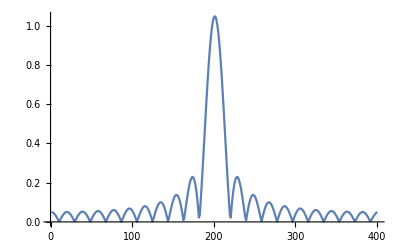

```mathematica
ListLinePlot[Abs[fw],PlotRange->All]
```

```mathematica
ifw=InverseFourier[fw];
```

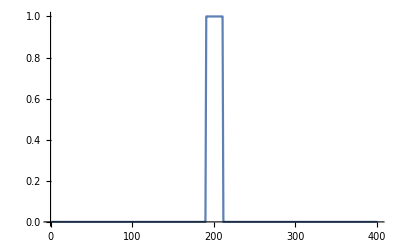

```mathematica
ListLinePlot[Abs[ifw],PlotRange->All]
```